```mathematica
a=1.061;
b=Sqrt[2]/2;
c=I*0.3536;
```

```mathematica
ts01=((2*a*b)/(a*b+b*c))^2
```

2.88035-2.15976 ⅈ

```mathematica
ts12=((2*b*c)/(b*c+a*b))^2
```

-0.319919+0.239882 ⅈ

```mathematica
rs01=((-a*b+b*c)/(a*b+b*c))
```

-0.800068+0.59991 ⅈ

```mathematica
(ts01)
```

2.88035-2.15976 ⅈ

```mathematica
z01=Sqrt[2.880352863898399^2+2.1597556653272614^2]
ArcTan[-2.1597556653272614/2.880352863898399]
```

3.60014

-0.643388

```mathematica
ts12
```

-0.319919+0.239882 ⅈ

```mathematica
z12=Sqrt[0.31991856278571157^2+0.23988238978631204^2 ]
ArcTan[0.23988238978631204/-0.31991856278571157]
```

0.399864

-0.643388

```mathematica
rs01
```

-0.800068+0.59991 ⅈ

```mathematica
z01=Sqrt[0.8000678566710275^2+0.5999095137783934^2]
ArcTan[0.5999095137783934/-0.8000678566710275]
```

1.

-0.643388

```mathematica
(Exp[-I*2.22*be]-Exp[-I*0.643]^2*Exp[-I*2.22*be])^2*Exp[I*0.643]^2
```

(-1.43808+1.11022×10^-16 ⅈ) ⅇ^((0.-4.44 ⅈ) be)

```mathematica
Exp[-I*2.22*be]*-Exp[-I*2.22be]
```

-ⅇ^((0.-4.44 ⅈ) be)

```mathematica
Exp[-I*0.634]^2
```

0.29819-0.954506 ⅈ

```mathematica
z01=Sqrt[0.29819048080147226^2+0.9545063840328083^2]
ArcTan[0.9545063840328083/-0.29819048080147226]*2
```

1.

-2.536

```mathematica
1-2*Exp[-1.268]+Exp[2.536]
```

13.0663

```mathematica
Exp[1.268]-2*Exp[-2.563]
```

3.39959

```mathematica
Abs[(ts01)]*Abs[(ts12)]
```

1.43957

```mathematica
(Abs[(ts01)]*Abs[(ts12)])/(Exp[I*2.22*d]-(rs01)*(rs01)*Exp[I*2.22*d])^2
```

(-0.280217-0.959937 ⅈ) ⅇ^((0.-4.44 ⅈ) d)

```mathematica
Sin[Pi/4]
```

1/(√2)

```mathematica
(((2*a*b)/(a*b+b*c))^2*((2*b*c)/(b*c+a*b))^2)
```

-0.403391+1.38189 ⅈ

```mathematica
(Exp[I*2.22*d]-((-a*b+b*c)/(a*b+b*c))*((b*c-a*b)/(b*c+a*b))*Exp[I*2.22*d])^2
```

(-0.403391+1.38189 ⅈ) ⅇ^((0.+4.44 ⅈ) d)

## Problem 4.7

```mathematica
lambda=3;
```

```mathematica
T=1.44/(Exp[4.44*d/lambda]+Exp[-4.44*d/lambda]-0.560);
```

```mathematica
data={{0,1},{.475,34/37},{1.09,13/37},{1.57,6/37},{2.03,3/37},{2.58,2.4/37},{3.05,1.1/37},{3.52,(.5)/37},{4.05,(.16)/37},{4.55,0.08/37},{5.08,0.04/37}};
```

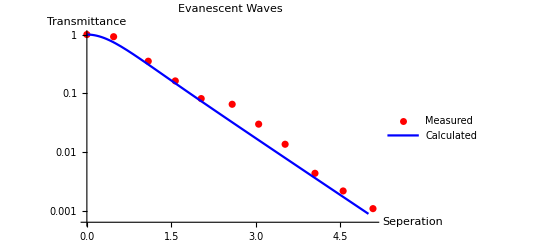

```mathematica
Show[ListLogPlot[data, PlotStyle->Red, PlotLegends->{"Measured"}],LogPlot[1.44/(Exp[4.44*d/lambda]+Exp[-4.44*d/lambda]-0.560),{d,0,5},PlotStyle->Blue,PlotLegends->{"Calculated"}],PlotLabel->"Evanescent Waves",AxesLabel->{"Seperation","Transmittance"}]
```